## Define Potential & Solve for Cosmological Parameters

```mathematica
(* Define an inflationary potential *)
left = False;
v[x_]:=(0.1)*(1+Log[x]); 
vp[x_]=v'[x];
vpp[x_] = v''[x];
ni = 80; (* initial value f n for integration *)
nf = -2.8; (* final value of n for integration *)
ni2 = 80;
nf2 = 0;
n1guess = -1;
ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False,left];
If[%===$Aborted,Print["ABORTED"],
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,True]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕ0list = {0.847412}

vacuumArray = {}

NDSolve::ndsz: At n == -1.40065, step size is effectively zero; singularity or stiff system suspected.

At n = 0, ϵ1 = 0.999885

ns[60] = 0.978928

r[60] = 0.0190286

```mathematica
(* Define an inflationary potential *)
left = False;
v[x_]:=(0.1)*(1+Log[x]+0.0001*x^4);
vp[x_]=v'[x];
vpp[x_] = v''[x];
ni = 80; (* initial value f n for integration *)
nf = -2.8; (* final value of n for integration *)
ni2 = 80;
nf2 = 0;
n1guess = -1;
ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,False,False,left];
If[%===$Aborted,Print["ABORTED"],
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,True]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕ0list = {0.847467}

vacuumArray = {}

NDSolve::ndsz: At n == -1.04614, step size is effectively zero; singularity or stiff system suspected.

At n = 0, ϵ1 = 1.

ns[60] = 1.00895

r[60] = 0.0732722

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

ϕ0list = {-0.573108,0.573108}

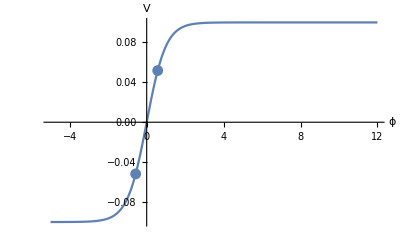

vacuumArray = {}

ϕ0 = 0.573108

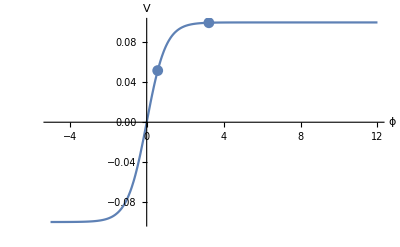

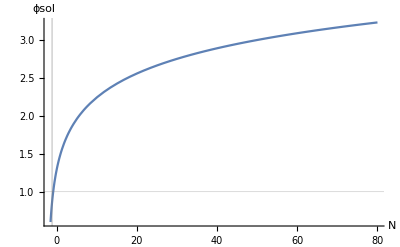

At n = 0, ϵ1 = 0.0354567

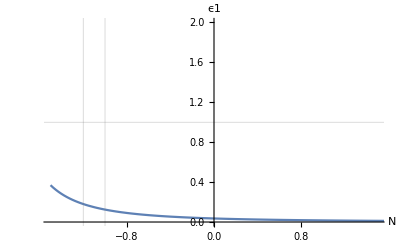

InterpolatingFunction::dmval: Input value {-5.13201} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2.36471} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.50835} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

At n1 = -1.77768, ϵ1 = 1.

ϕi2 = 3.2223

ϕpi2 = 0.00632991

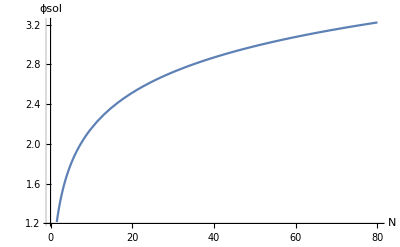

ϕsol2[60] = 3.07643

At n = 0, ϵ1 = 1.02097

ns[60] = 0.966263

r[60] = 0.000572863

```mathematica
(* Define an inflationary potential *)
left = False;
v[x_]:=(0.1)*(Tanh[x]);
vp[x_]=v'[x];
vpp[x_] = v''[x];
ni = 80; (* initial value f n for integration *)
nf = -1.5; (* final value of n for integration *)
ni2 = 80;
nf2 = 0;
n1guess = -1;
ϕsol2=findϕsol[v,vp,vpp,ni,nf,ni2,nf2,n1guess,True,True,left];
If[%===$Aborted,Print["ABORTED"],
{ns,r,ϵ2} = findNsR[v,vp,ϕsol2,ni2,nf2,False,True]];
```